```mathematica
"
```

```mathematica
Directory[]
```

/home/rui/prc2/simulaciones/sim_2do_cuatri/pruebas-rui/plots

```mathematica
lts
```

```mathematica
FilePrint["r_out.txt"]
```

```mathematica
vo1G=SemanticImport[ "r_out_rl=1g.txt"][All, {2->parseComplexLTSpice}];//Quiet
```

```mathematica
vo2=SemanticImport[ "r_out_rl=2.txt"][All, {2->parseComplexLTSpice}];//Quiet
```

```mathematica
vo1Gts=ro1G[All, Values][TimeSeries];
vo2ts=ro2[All, Values][TimeSeries];
```

v_o=R_L/(R_L+r_o)v_T

```mathematica
Solve[{vout1==rl1/(rl1+ro)vt , vout2==rl2/(rl2+ro)vt}, ro, Reals]
```

{}

```mathematica
Block[{rl1, rl2, vout1, vout2},
ro[vout1_, vout2_]=(rl1 rl2 (vout1-vout2))/(-rl2 vout1+rl1 vout2)/.{rl1->2, rl2->1*^9};
]
```

```mathematica
SetAttributes[ro, Listable];
```

```mathematica
TimeSeriesMapThread[ro, {vo2ts,vo1Gts}]//Head
```

List

```mathematica
vo2ts
```

```mathematica
ro[vo1Gts+vo2ts]
```

ro[TimeSeries[…]]

```mathematica
r=TimeSeriesThread[ro@*Apply[Sequence], {vo2ts,vo1Gts}];
```

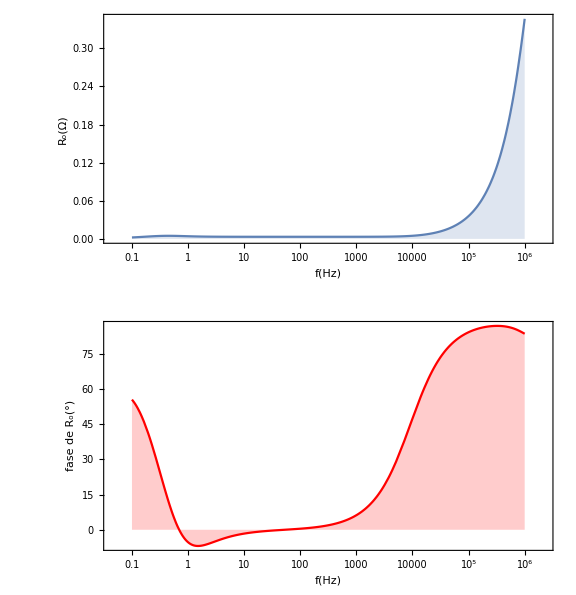

```mathematica
gr=GraphicsColumn[{
LogLinearPlot[Abs@r[f], {f, 0.1, 1000000},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, FrameLabel->{"f(Hz)","R_o(Ω)"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}],
LogLinearPlot[(Arg@r[f])/Degree, {f, 0.1, 1000000},Filling->0,PlotRange->Full,PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, PlotStyle->Red,FrameLabel->{"f(Hz)","fase de R_o("<>ToString[Degree, StandardForm]<>")"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
}, ImageSize->Large
]
```

```mathematica
Export["../../../../informe/img/sim/R_out.pdf", gr];
```

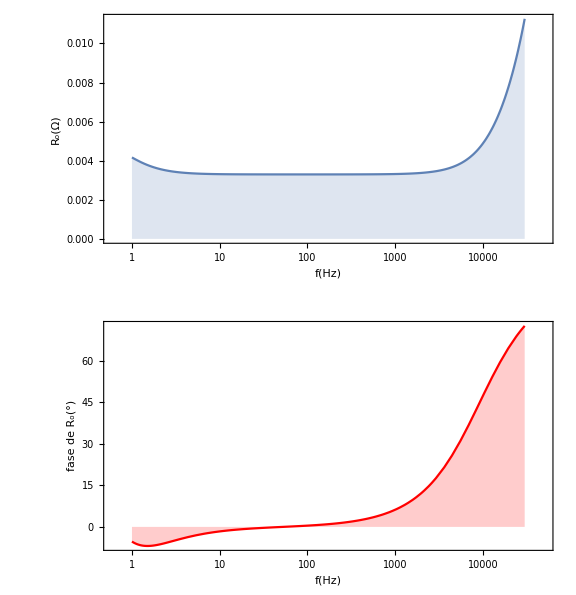

```mathematica
gr=GraphicsColumn[{
LogLinearPlot[Abs@r[f], {f, 1, 30000},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, FrameLabel->{"f(Hz)","R_o(Ω)"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}],
LogLinearPlot[(Arg@r[f])/Degree, {f, 1, 30000},Filling->0,PlotRange->Full,PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, PlotStyle->Red,FrameLabel->{"f(Hz)","fase de R_o("<>ToString[Degree, StandardForm]<>")"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
}, ImageSize->Large
]
```

```mathematica
TimeSeriesWindow[r,{1,30000}]//Mean/*Abs
```

0.00348364

```mathematica
TimeSeriesWindow[r,{1,30000}]//Mean@*Abs
```

0.0038601

```mathematica
TimeSeriesWindow[r,{1,30000}]//MinMax@*Arg/*(# /Degree&)
```

{-6.90256,72.201}

```mathematica
Export["../../../../informe/img/sim/R_out-zoom.pdf", gr];
```

## Fuente corriente

```mathematica
parseComplexLTSpice[sam_]:=StringReplace[sam,StartOfString~~ "("~~mag:Longest[Except["d"]..]~~"dB,"~~phase___~~"°)"~~EndOfString:>{mag, phase}]//First/*Interpreter["Number"]/*ReplaceAll[
{mag_, phase_}:>10^(mag/20) Exp[I Degree phase]
]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
vo2=SemanticImport[ "r_out-current.txt"][All, {2->parseComplexLTSpice}];//Quiet
```

```mathematica
la=SemanticImport[ "r_out-current.txt"];
vo2=la[All, {2->parseComplexLTSpice}];
```

```mathematica
r=vo2[All,Values][TimeSeries];
```

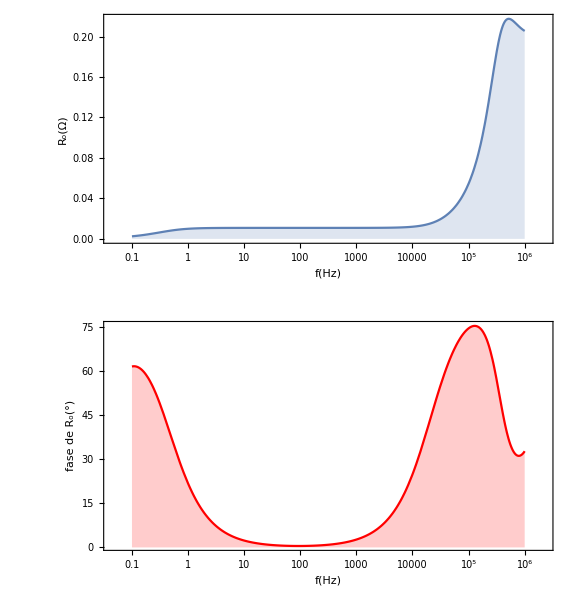

```mathematica
gr=GraphicsColumn[{
LogLinearPlot[Abs@r[f], {f, 0.1, 1000000},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, FrameLabel->{"f(Hz)","R_o(Ω)"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}],
LogLinearPlot[(Arg@r[f])/Degree, {f, 0.1, 1000000},Filling->0,PlotRange->Full,PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, PlotStyle->Red,FrameLabel->{"f(Hz)","fase de R_o("<>ToString[Degree, StandardForm]<>")"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
}, ImageSize->Large
]
```

```mathematica
Export["../../../../informe/img/sim/R_out.pdf", gr];
```

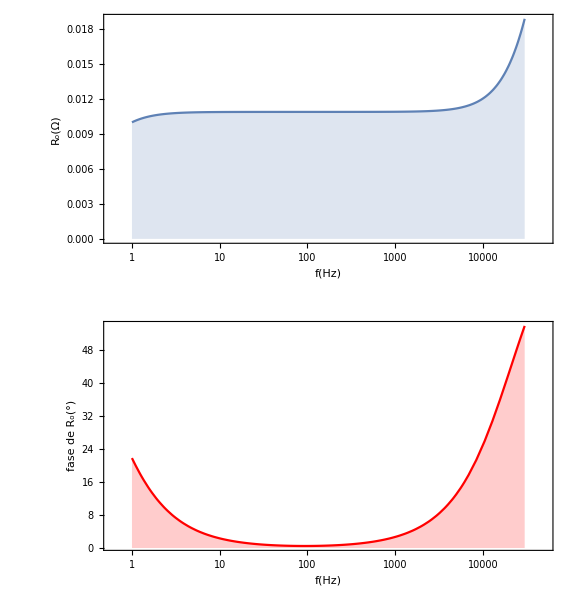

```mathematica
gr=GraphicsColumn[{
LogLinearPlot[Abs@r[f], {f, 1, 30000},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, FrameLabel->{"f(Hz)","R_o(Ω)"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}],
LogLinearPlot[(Arg@r[f])/Degree, {f, 1, 30000},Filling->0,PlotRange->Full,PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, PlotStyle->Red,FrameLabel->{"f(Hz)","fase de R_o("<>ToString[Degree, StandardForm]<>")"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
}, ImageSize->Large
]
```

```mathematica
Export["../../../../informe/img/sim/R_out-zoom.pdf", gr];
```

```mathematica
Export["../../../../informe/img/sim/R_out.pdf", gr];
```

```mathematica
NIntegrate[r[f], {f, 1, 30000}]/29999//Abs
```

0.0133189

```mathematica
Arg[r[100000]]/Degree
```

74.6884

```mathematica
NArgMax[{Arg[r[f]], f>50000},f]
```

50033.6

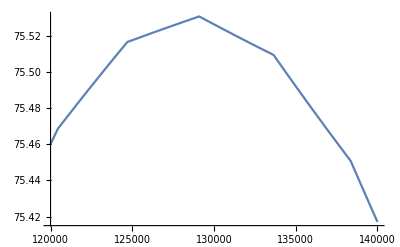

```mathematica
Plot[Arg[r[f]]/Degree, {f, 120000, 140000}]
```

```mathematica
;
```

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[], "..","..","final-cursada", "data"}]]
```

/home/rui/prc2/simulaciones/sim_2do_cuatri/final-cursada/data

```mathematica
parseComplexLTSpice["1.00000000000000e-001	(-5.19103727297599e+001dB,6.16896025594902e+001°)"]
```

```mathematica
la[2,2]
```

(-5.16454083991561e+001dB,6.17444677795317e+001°)

```mathematica
10^(-51.6/20) Exp[I 61.7 Degree]
```

0.00124698+0.00231589 ⅈ

```mathematica
10^(-51.6/20) Exp[I 61.7 Degree]//Abs
```

0.00263027

```mathematica
la[2,2]//parseComplexLTSpice
```

0.00123869+0.00230478 ⅈ

```mathematica
"(-3.83671112228926e+001dB,2.55113439511351e+001°)"//parseComplexLTSpice/*Abs
```

0.0120683

```mathematica
la[333;;336,1]
```

{ 9933.,10280.,10650.,11020. }
1 level | 4elementsDataset[{__Real}]

```mathematica
vo2[334, 2]
```

0.0108916+0.00519767 ⅈ

```mathematica
la[334,2]//parseComplexLTSpice
```

0.0108916+0.00519767 ⅈ

```mathematica
10^(-38.367/20)
```

0.0120684

```mathematica
FilePrint["r_out.txt"]
```

```mathematica
10^(-39.2785367622075/20)
```

0.0108661

```mathematica
la=SemanticImport[ "r_out.txt"];
vo2=la[All, {2->parseComplexLTSpice}];
```

$CharacterEncoding::utf8: The byte sequence {176} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding::utf8 will be suppressed during this calculation.

```mathematica
vo2[All, {2->Abs}]
```

Freq. | V(n001)/1A
0.1 | 0.002538
0.1035 | 0.002617
0.1072 | 0.002698
0.111 | 0.002781
0.1149 | 0.002868
0.1189 | 0.002956
0.1231 | 0.003048
0.1275 | 0.003142
0.132 | 0.003239
0.1366 | 0.003338
0.1414 | 0.00344
0.1464 | 0.003545
0.1516 | 0.003652
0.1569 | 0.003762
0.1625 | 0.003875
0.1682 | 0.00399
⋮_451 | 
2 levels | 467rows | Dataset[{__Association}]

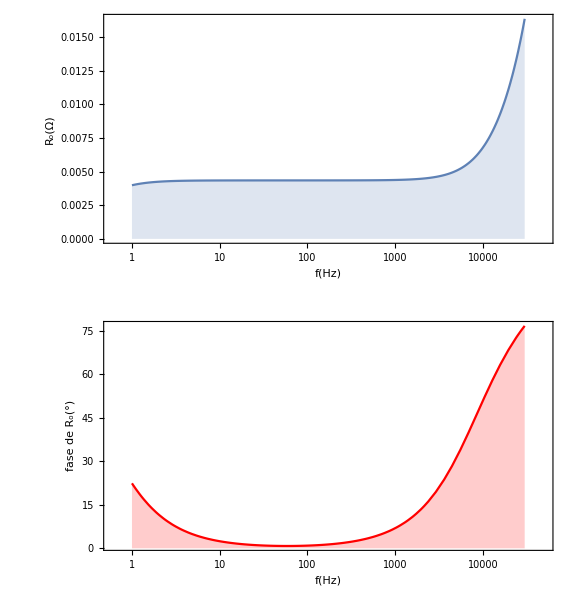

```mathematica
gr=GraphicsColumn[{
LogLinearPlot[Abs@r[f], {f, 1, 30000},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, FrameLabel->{"f(Hz)","R_o(Ω)"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}],
LogLinearPlot[(Arg@r[f])/Degree, {f, 1, 30000},Filling->0,PlotRange->Full,PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, PlotStyle->Red,FrameLabel->{"f(Hz)","fase de R_o("<>ToString[Degree, StandardForm]<>")"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
}, ImageSize->Large
]
```

```mathematica
gr=GraphicsColumn[{
LogLinearPlot[Abs@r[f], {f, 1, 30000},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, FrameLabel->{"f(Hz)","R_o(Ω)"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}],
LogLinearPlot[(Arg@r[f])/Degree, {f, 1, 30000},Filling->0,PlotRange->Full,PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, PlotStyle->Red,FrameLabel->{"f(Hz)","fase de R_o("<>ToString[Degree, StandardForm]<>")"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
}, ImageSize->Large
]
```

```mathematica
vi=SemanticImport[ "r_in.txt"][All, {2->parseComplexLTSpice}];//Quiet
```

```mathematica
ri=vi[All,Values][TimeSeries];
```

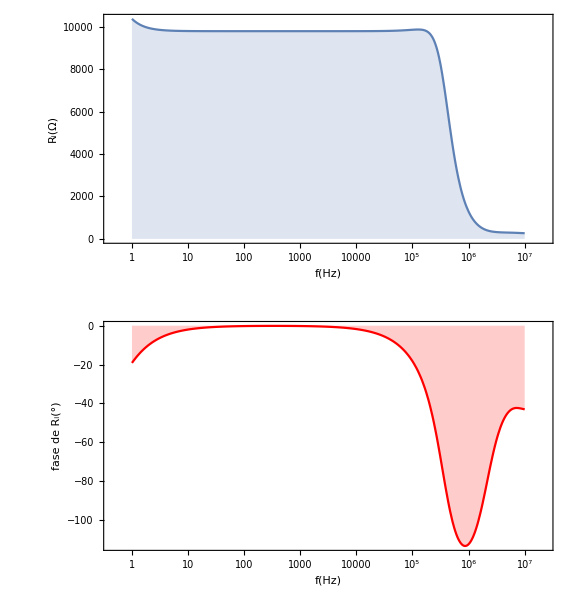

```mathematica
gr=GraphicsColumn[{
LogLinearPlot[Abs@ri[f], {f, 1, 1*^7},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, FrameLabel->{"f(Hz)","R_i(Ω)"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}],
LogLinearPlot[(Arg@ri[f])/Degree, {f, 1, 1*^7},Filling->0,PlotRange->Full,PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, PlotStyle->Red,FrameLabel->{"f(Hz)","fase de R_i("<>ToString[Degree, StandardForm]<>")"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
}, ImageSize->Large
]
```

```mathematica
Export["../../../../informe/img/sim/R_i.pdf", gr];
```

```mathematica
NIntegrate[ri[f], {f, 1, 30000}]/29999//Abs
```

9798.89

```mathematica
NIntegrate[r[f], {f, 1, 30000}]/29999//Abs
```

0.0133189

```mathematica
NIntegrate[r[10^f], {f, Log10[1], Log10@30000}]/(Log10[30000]-Log10[1])//Abs
```

0.0109532

```mathematica
NIntegrate[ri[10^f], {f, Log10[1], Log10@30000}]/(Log10[30000]-Log10[1])//Abs
```

9807.27

```mathematica
bodefrec=SemanticImport[ "resp-frec.txt"][All, {2->parseComplexLTSpice}];//Quiet
bodefrec=bodefrec[All,Values][TimeSeries];
```

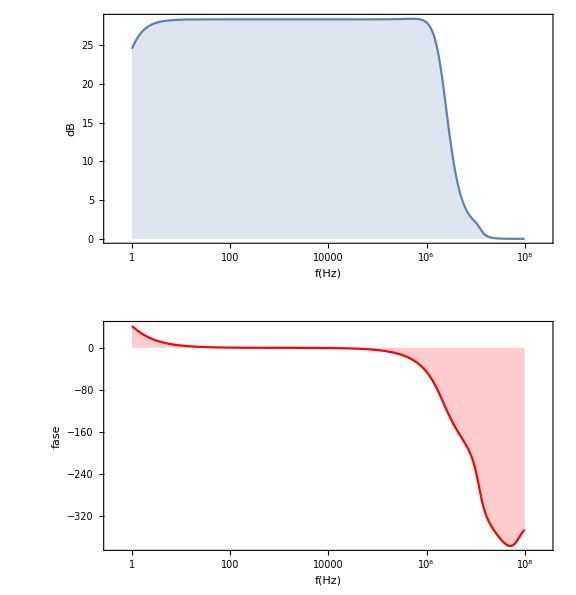

```mathematica
gr=GraphicsColumn[{
LogLinearPlot[Abs@bodefrec[f], {f, 1, 1*^8},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,1}}, FrameLabel->{"f(Hz)","dB"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}],
LogLinearPlot[If[f<2 10^6,(Arg@bodefrec[f])/Degree,Mod[(Arg@bodefrec[f])/Degree,360, -400]], {f, 1, 1*^8},Filling->0,PlotRange->Full,PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, PlotStyle->Red,FrameLabel->{"f(Hz)","fase"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
}, ImageSize->Large
]
```

```mathematica
Export["../../../../informe/img/sim/bode.pdf", gr];
```

```mathematica
(20*^6)/(40 2 π)//N
```

79577.5

0.036%@500
0.04%@500
0.039%@2kHz
0.035%@5kHz
0.037%@10kHz
0.035%@20kHz
0.03%@30kHz
0.03%@40kHz
0.06%@50kHz
0.13%@60kHz
0.3%@70kHz
0.65% a 80kHz
1.66% 90k
3.78%@100kHz
8%@120kHz

```mathematica
bode=TimeSeries[{{20, 0.062}, {50, 0.032}, {100, 0.035}, {200, 0.036}, {500, 0.04}, {2000, 0.039}, {5000, 0.035}, {10000, 0.037}, {20000, 0.035}, {30000, 0.03}, {40000, 0.03}, {50000, 0.06}, {60000, 0.13}, {70000, 0.3}, {80000, 0.65}, {90000, 1.66}, {100000, 3.78}, {120000, 8}, {200000, 11}, {500000, 11.44}}];
```

12% es la de la onda triangular

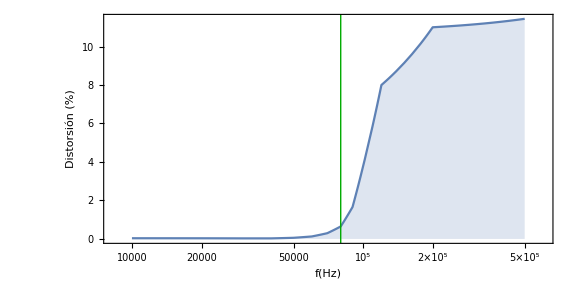

```mathematica
gr=LogLinearPlot[bode[f], {f, 10000, 500000},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,1}}, FrameLabel->{"f(Hz)","Distorsión (%)"}, ImageSize->Large,Epilog->{Darker@Green,InfiniteLine[{Log[80000], 0}, {0, 1}]},AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
```

```mathematica
gr=LogLinearPlot[bode[f], {f, 20, 30000},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0.01}}, FrameLabel->{"f(Hz)","Distorsión (%)"}, ImageSize->Large,Epilog->{Darker@Green,InfiniteLine[{Log[80000], 0}, {0, 1}]},AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
```

```mathematica
Export["/home/rui/prc2/informe/img/sim/distorsion-frec.pdf", gr];
```

```mathematica
NotebookDirectory[]
```

/home/rui/prc2/simulaciones/sim_2do_cuatri/pruebas-rui/plots/

## 1era etapa

```mathematica
bode1era=SemanticImport[ "1era-etapa.txt"][2;;, {2->parseComplexLTSpice,3->parseComplexLTSpice}];//Quiet
bode1era=bode1era[All,Values][TimeSeries];
```

```mathematica
bode1era=SemanticImport[ "1era-etapa.txt"][2;;, {2->parseComplexLTSpice,3->parseComplexLTSpice}];//Quiet
```

```mathematica
ts1=bode1era[All, Values][All, ;;2][TimeSeries];
ts2=bode1era[All, Values][All, {1,3}][TimeSeries];
```

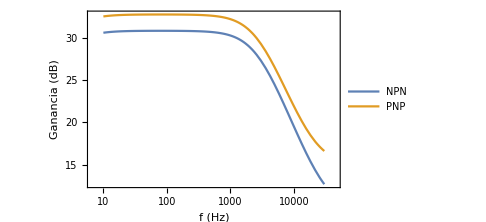

```mathematica
LogLinearPlot[20 Log10@{Abs[ts1][f],Abs[ts2][f]}//Evaluate, {f, 10,30000}, PlotTheme->"Detailed", PlotRangePadding->{{-0.8,-0.8},{-5,1}}, ImageSize->Medium, PlotLegends->Placed[{"NPN", "PNP"}, {Right, Top}], FrameLabel->{"f (Hz)", "Ganancia (dB)"}]
```

```mathematica
20 Log10@Max[Abs@ts1]
```

30.7915

```mathematica
20 Log10@Max[Abs@ts2]
```

32.7165

## 2da etapa

```mathematica
bode2da=SemanticImport[ "2da-etapa.txt"][2;;, {2->parseComplexLTSpice,3->parseComplexLTSpice}];//Quiet
```

```mathematica
ts1=bode2da[All, Values][All, ;;2][TimeSeries];
ts2=bode2da[All, Values][All, {1,3}][TimeSeries];
```

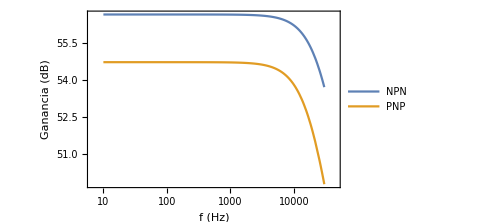

```mathematica
LogLinearPlot[20 Log10@{Abs[ts1][f],Abs[ts2][f]}//Evaluate, {f, 10,30000}, PlotTheme->"Detailed", PlotRangePadding->{{-0.8,-0.8},{-1,2}}, ImageSize->Medium, PlotLegends->Placed[{"NPN", "PNP"}, {Right, Top}], FrameLabel->{"f (Hz)", "Ganancia (dB)"}]
```

```mathematica
20 Log10@Max@Abs@ts1
```

56.6345

```mathematica
20 Log10@Max@Abs@ts2
```

54.7096